# Иваненко Иван, Лабораторная работа #1 1.1 1. Используя функцию Range создайте список {1, 2, 3, 4}

```mathematica
Range[4]
```

{1,2,3,4}

## 2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

## 3. Используя функции Range и Reverse, создайте список {4,3,2,1}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

## 4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

## 5. Используя функции Range, Reverse и Join, создайте список {1,2,3,4,4,3,2,1}

```mathematica
Join[Range[4], Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

## 6. Нарисовать график списка чисел, которые возрастают от 1 до 100, а затем убывают от 100 до 1

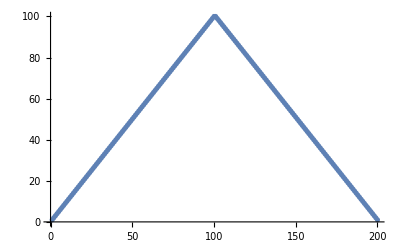

```mathematica
ListPlot[Join[Range[100], Reverse[Range[100]]]]
```

## 7. Используя функции Range и RandomInteger создайте список случайно генерированной длины, не превышающей число 10

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4}

## 8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]]

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

## 9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]

```mathematica
Range[5]
```

{1,2,3,4,5}

## 10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

## 11. Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]

```mathematica
Join[Range[20], Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

## 1.2 Строки и Текст 1. Присоедините две копии строки «Здравствуйте»

```mathematica
StringJoin["Здравствуйте", "Здравствуйте"]
```

ЗдравствуйтеЗдравствуйте

## 2. Создайте единую строку всего английского алфавита заглавными буквами.

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

## 3. Сгенерируйте строку английского алфавита в обратном порядке.

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

## 4. Объедините 100 копий строки «ABCD»

```mathematica
StringRepeat["ABCD", 100]
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

## 5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]], 6]
```

abcdef

## 6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих число букв (включая пробелы) равное номеру элемента.

```mathematica
Column[Table[StringTake["это о строках", i], {i, StringLength["это о строках"]}]]
```

```mathematica
{{"э"}, {"эт"}, {"это"}, {"это "}, {"это о"}, {"это о "}, {"это о с"}, {"это о ст"}, {"это о стр"}, {"это о стро"}, {"это о строк"}, {"это о строка"}, {"это о строках"}}
```

## 7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

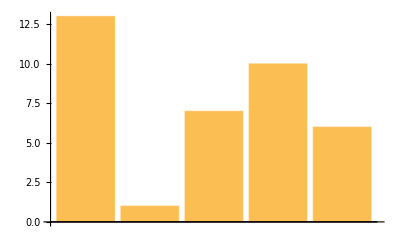

```mathematica
BarChart[StringLength[StringSplit["Давным-давно, в далекой галактике, далеко"]]]
```

## 8. Найдите максимальную длину слова среди английских слов из WordList[]

```mathematica
Max[StringLength[WordList[]]]
Pick[WordList[],StringLength[WordList[]],Max[StringLength[WordList[]]]]
```

23

{electroencephalographic}

## 9. Используйте Length, чтобы найти длину русского алфавита

```mathematica
Length[Alphabet["Russian"]]
```

33

## 10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
StringReverse[ToUpperCase[StringJoin[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

## 1.3 1. Используйте Range и чистую функцию для создания списка из квадратов первых 20 натуральных чисел.

```mathematica
Range[20]^2
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

## 2. Составьте список из результатов смешивания желтого, зеленого и синего цветов с красным цветом.

```mathematica
Blend[{#, Red}] &/@{Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

## 3. Создайте список столбцов в рамках, содержащих прописные и строчные версии каждой буквы алфавита.

```mathematica
Framed[Column[{ToLowerCase[#], ToUpperCase[#]}]] &/@ Alphabet[]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

## 4. Составьте список букв алфавита в случайных цветах в рамках, имеющих случайные цвета фона

```mathematica
Style[Framed[#], RandomColor[], Background -> RandomColor[]] &/@ Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

## 5. Напишите в более простой форме команду (#^2+1&)/@Range[10]

```mathematica
Range[10]^2 + 1
```

```mathematica
{2,5,10,17,26,37,50,65,82,101}
```

## 1.4 Композиции функций и их программирование 1. Составьте список результатов использования функции Blur до 10 раз, начиная с растрированного размера 30 “X” (Используйте: Rasterize[Style]

```mathematica
NestList[Blur, Rasterize[x, RasterSize -> 30], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 2. Начните с x, затем создайте список, использовав последовательно функцию Framed до 10 раз, используя каждый раз случайный цвет фона.

```mathematica
NestList[Framed[#, Background -> RandomColor[]] & , x, 10]
```

{x,x,x,x,x,x,x,x,x,x,x}

## 3. Начните с размера 50 для “A”, затем создайте список вложенного применения Framed и случайного вращения 5 раз.

```mathematica
NestList[Rotate[Framed[#], Random[]] &, Style["A", FontSize -> 50], 5]
```

{A,A,A,A,A,A}

## 4. Создайте линейный график из 100 итераций логического итерационного отображения 4 # (1 - #) &, начиная с 0.2

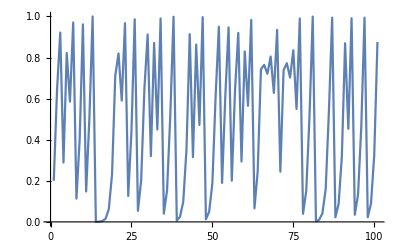

```mathematica
ListLinePlot[NestList[4 # (1 - #) &, 0.2, 100]]
```

## 5. Найдите числовое значения результата из 30 итераций применения функции 1 + 1 / # &, начиная с 1

```mathematica
Last[NestList[1 + 1 / # &, 1, 30]]
```

2178309/1346269

## 6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения

```mathematica
Table[3^(i-1),{i,10}]
```

{1,3,9,27,81,243,729,2187,6561,19683}

## 7. Составьте список результатов действия вложенной функции (метод Ньютона) (# + 2 / #) / 2 до 5 раз, начиная с 1.0, а затем вычтите 2 из всех результатов.

```mathematica
# - Sqrt[2]&/@ NestList[# + 2 / # &, 1.0, 5]
NestList[# + 2 / # &, 1.0, 5]
```

{-0.414214,1.58579,2.25245,2.79791,3.27273,3.69945}

{1.,3.,3.66667,4.21212,4.68694,5.11366}

## 8. Создайте список из 5 степеней числа 2, т.е. 2 ^ 2 ^ 2 ... ^ 2 n раз, причем n меняется от 0 до 4.

```mathematica
Table[NestList[#  ^ 2 &, 2,  RandomInteger[4]], {i, 5}]
```

{{2,4},{2,4},{2},{2,4,16,256},{2}}

## 1.5 Определение функций пользователя

## 1. Определите функцию f, которая вычисляет квадрат ее аргумента

```mathematica
f[arg_] := arg ^ 2
f[5]
```

25

## 2. Определить функцию poly, которая имеет целочисленное значение аргумента и создает изображение оранжевого правильного многоугольнка с числом сторон, равным значению этого аргемента.

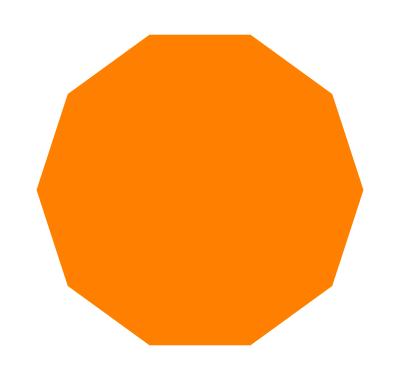

RegularPolygon[10]

```mathematica
poly[x_] := Graphics[{Orange, RegularPolygon[x]}]
poly[10]
RegularPolygon[10]
```

## 3. Определите функцию f, которая берет список из двух элементов и помещает их в обратном порядке

```mathematica
f[list_] := Reverse[list]
f[Range[2]]
```

{2,1}

## 4. Определите функцию f, которая имеет два аргумента и дает результат в виде дроби, где числитель равен произведению этих элементов, а знаменатель - их сумме

```mathematica
f[a_, b_] := (a * b)/(a + b)
f[5, 10]
```

10/3

## 5. Определите функцию f, которая имеет два аргумента и дает результат в виде списка трех элементов, которые соответственно равны сумме, разности и частному этих аргументов

```mathematica
f[a_, b_] := {a + b, a - b, a / b}
f[5, 10]
```

{15,-5,1/2}

## 6. Определите функцию evenodd, которая зависит от одного целочисленного аргумента и имеет значение Black, если ее аргумент четный, значение White, в противном случае, значение Red - если аргумент равен нулю

```mathematica
Evenodd[x_] := If[x == 0, Red, If[EvenQ[x], Black, White]]
Evenodd[0]
Evenodd[1]
Evenodd[2]
```

RGBColor[1, 0, 0]

GrayLevel[1]

GrayLevel[0]

## 7. Определите функцию fibonacci f с f[0] = 1 и f[1] = 1, а f[n] для натурального числа n является суммой f[n - 1] и f[n - 2]

```mathematica
Fib[x_] := If[x == 0  || x == 1 || x == 2, 1, Fib[x - 1] + Fib[x  -2 ]]
Fib[0]
Fib[1]
Fib[10]
Fibonacci[10]
```

1

1

55

55